# Hermite interpolation approach in 1D To solve elliptic PDE

## Source Function

Original function

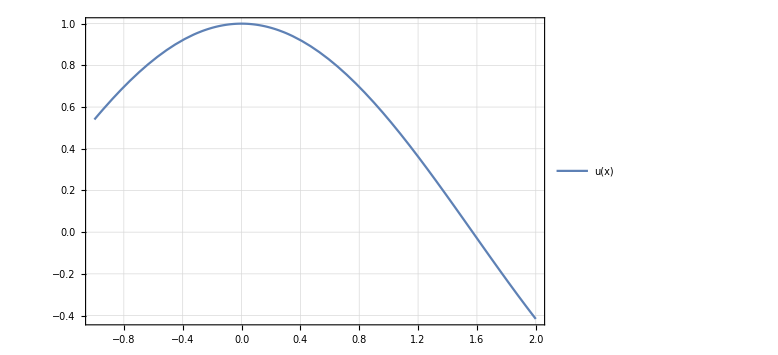

```mathematica
u[x_]=Cos[x];
f[x_]=Laplacian[u[x],{x}];
li=0.;(* Inferior limit *)
ls=1.;(* Superior limit*)
Print[Style["Original function",25,Blue]]
Plot[u[x],{x,li-1,ls+1},PlotRange->All,PlotTheme->"Detailed",ImageSize->Large]
```

## Input data

```mathematica
(* Create mesh: First interior points, after exterior points *)
dx=0.01;(* Width of mesh *)
data=Range[li+dx,ls-dx,dx];
AppendTo[data,li];
AppendTo[data,ls];
ndata=Dimensions[data][[1]];
```

## Computing derivatives of RBFs

```mathematica
ϵ=1.0;
ϕ[r_]=Exp[-(ϵ r)^2];
r[x_]=Sqrt[x^2];

(* Computing derivatives *)
λ1=FullSimplify[ϕ[r[x-ξ]]]
λ2=FullSimplify[Laplacian[ϕ[r[x-ξ]],{ξ}]]
λ3=FullSimplify[Laplacian[λ1,{x}]]
λ4=FullSimplify[Laplacian[λ2,{x}]]
```

ⅇ^(-1. (x-1. ξ)^2)

ⅇ^(-1. (x-1. ξ)^2) (-2.+4. x^2-8. x ξ+4. ξ^2)

ⅇ^(-1. (x-1. ξ)^2) (-2.+4. x^2-8. x ξ+4. ξ^2)

ⅇ^(-1. (x-1. ξ)^2) (12.+16. x^4-64. x^3 ξ-48. ξ^2+16. ξ^4+x ξ (96.-64. ξ^2)+x^2 (-48.+96. ξ^2))

## Building interpolation matrix A

```mathematica
(* Generating interpolation matrix A *)
A=RandomReal[{0,1},{ndata,ndata}];
For[i=1,i≤ndata,i++,
For[j=1,j≤ndata,j++,
px=data[[i]];
py=data[[j]];
If[i≤ndata-2,
If[j≤ndata-2, A[[i,j]]=λ4/.x->px/.ξ->py,
A[[i,j]]=λ3/.x->px/.ξ->py],
If[j≤ndata-2,A[[i,j]]=λ2/.x->px/.ξ->py,
A[[i,j]]=λ1/.x->px/.ξ->py]
]
]
]
```

## Some characteristics of A

Condition number, determinant and matrix plot

8.32399×10^19

3.39236893811129×10^-1252

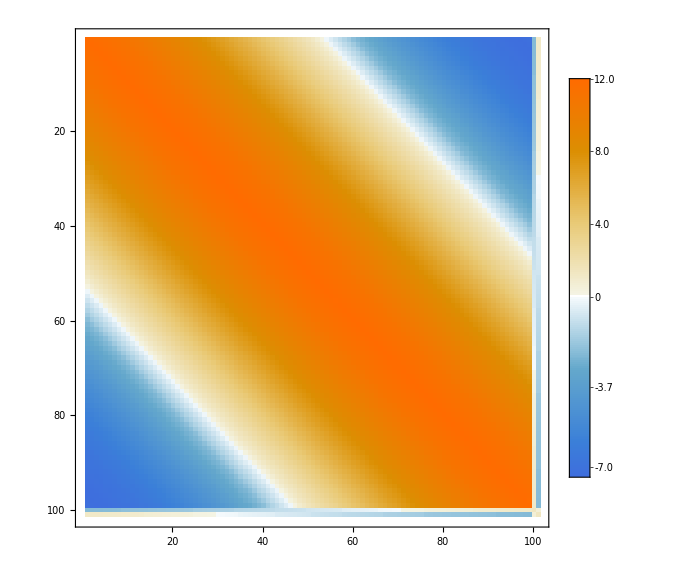

```mathematica
(* Matrix Information *)
Print[Style["Condition number, determinant and matrix plot",25,Blue]]
LinearAlgebra`MatrixConditionNumber[A,Norm->Infinity]
Det[A]
MatrixPlot[A,PlotTheme->"Detailed",ImageSize->Large]
```

## Building v: Ac=v

```mathematica
(* Building v:  A.c=v *)
v={};
For[i=1,i≤ndata,i++,
If[i≤ndata-2,AppendTo[v,f[data[[i]]]],
If[i==ndata-1,AppendTo[v,u[li]],
AppendTo[v,u[ls]]
]
]
]
```

## Solving the linear system

```mathematica
(* Solve the system *)
c=LinearSolve[A,v];
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{12., 11.994, 11.976, 11.9461, 11.9042, 11.8504, 11.7849, 11.7077, 11.6189, 11.5186, 11.407, 11.2842, « 27 », 4.35408, 4.0303, 3.70509, 3.37884, 3.05196, 2.72484, 2.39787, 2.07145, 1.74595, 1.42176, 1.09926, « 51 »}, {11.994, « 49 », « 51 »}, « 48 », « 51 »} may contain significant numerical errors.

## Building the interpolation function

```mathematica
(* Building interpolation function Pf *)
P=0;
For[i=1,i≤ndata,i++,
d=data[[i]];
If[i≤ndata-2,P+=c[[i]]λ2/.ξ->d,
P+=c[[i]]λ1/.ξ->d]
]
Pf[x_]=P;
Error[x_]=Pf[x]-u[x];
```

## Final Results

Interpolation function and Error function

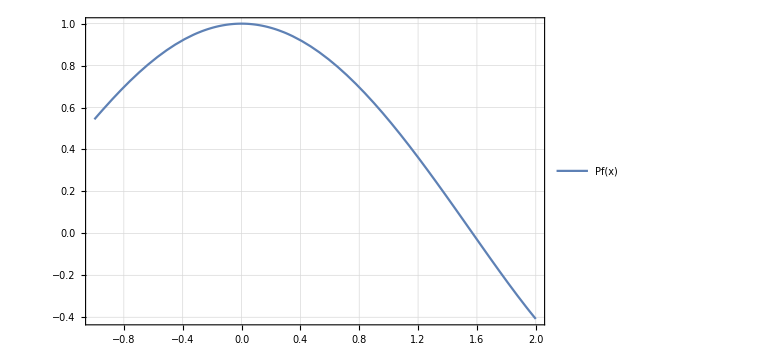

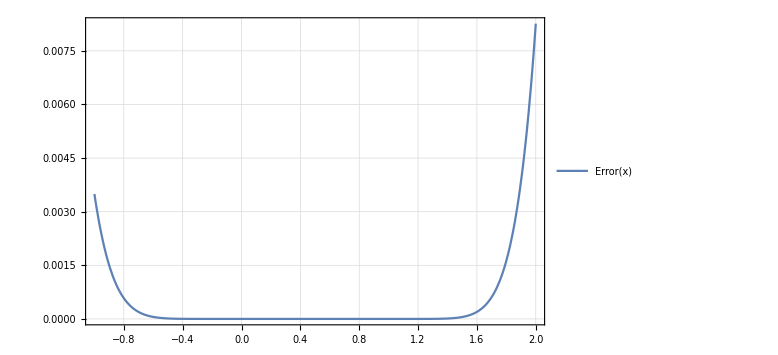

RMS error

9.21537×10^-18

```mathematica
Print[Style["Interpolation function and Error function",25,Blue]]
Plot[Pf[x],{x,li-1,ls+1},PlotRange->All,PlotTheme->"Detailed",ImageSize->Large]
Plot[Error[x],{x,li-1,ls+1},PlotRange->All,PlotTheme->"Detailed",ImageSize->Large]

(* RMS error *)
Print[Style["RMS error",25,Blue]]
NIntegrate[(Error[x])^2,{x,0,1},{y,0,1}]
```